## One Mode Approximation

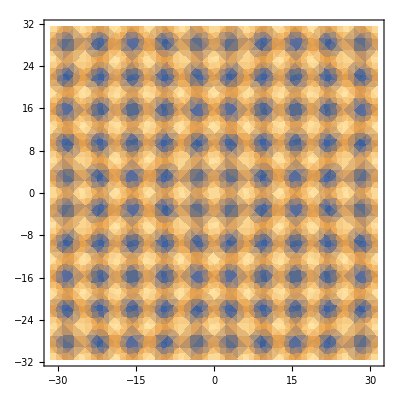

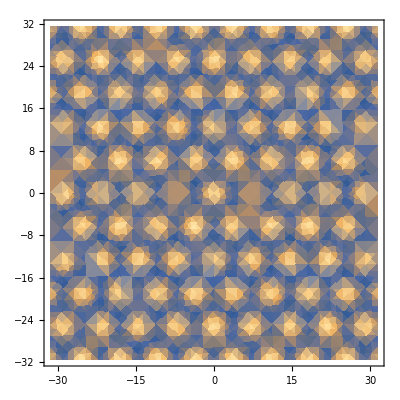

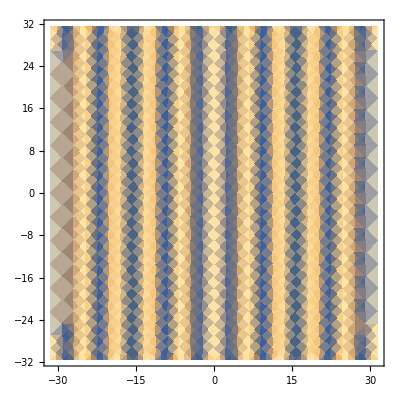

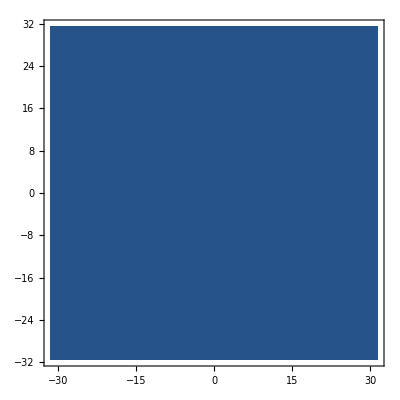

```mathematica
nsq[n_,A_,a_,x_,y_]=n+A*(Cos[(2π)/a x]+Cos[(2π)/a y]);
ntr[n_,A_,a_,x_,y_]=n+A*(Cos[(√3 π)/a x]Cos[π/a y]+1/2 Cos[(2π)/a y]);
nst[n_,A_,a_,x_,y_]=n+A*(Cos[(2π)/a x]);
nlq[n_,A_,a_,x_,y_]=n;
DensityPlot[nsq[0.0,1.0,2π,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[ntr[0.0,1.0,2π,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[nst[0.0,1.0,2π,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[nlq[0.0,1.0,2π,x,y],{x,-10π,10π},{y,-10π,10π}]
```

## The Simplest PFC Model

F(n)=∫ϵ n^2/2+n^4/4+n/2(1+∇^2)^2 nⅆx

### The Integrand

```mathematica
gsq[n_,A_,a_,ϵ_,x_,y_]=ϵ*nsq[n,A,a,x,y]^2/2+nsq[n,A,a,x,y]^4/4+nsq[n,A,a,x,y]/2*(nsq[n,A,a,x,y]+2*Laplacian[nsq[n,A,a,x,y],{x,y}]+Laplacian[Laplacian[nsq[n,A,a,x,y],{x,y}],{x,y}]);
gtr[n_,A_,a_,ϵ_,x_,y_]=ϵ*ntr[n,A,a,x,y]^2/2+ntr[n,A,a,x,y]^4/4+ntr[n,A,a,x,y]/2*(ntr[n,A,a,x,y]+2*Laplacian[ntr[n,A,a,x,y],{x,y}]+Laplacian[Laplacian[ntr[n,A,a,x,y],{x,y}],{x,y}]);
gst[n_,A_,a_,ϵ_,x_,y_]=ϵ*nst[n,A,a,x,y]^2/2+nst[n,A,a,x,y]^4/4+nst[n,A,a,x,y]/2*(nst[n,A,a,x,y]+2*Laplacian[nst[n,A,a,x,y],{x,y}]+Laplacian[Laplacian[nst[n,A,a,x,y],{x,y}],{x,y}]);
glq[n_,A_,a_,ϵ_,x_,y_]=ϵ*nlq[n,A,a,x,y]^2/2+nlq[n,A,a,x,y]^4/4+nlq[n,A,a,x,y]/2*(nlq[n,A,a,x,y]+2*Laplacian[nlq[n,A,a,x,y],{x,y}]+Laplacian[Laplacian[nlq[n,A,a,x,y],{x,y}],{x,y}]);
```

### The Free Energy per Area (free energy density)

```mathematica
fsq[n_,A_,a_,ϵ_]=Integrate[Integrate[gsq[n,A,a,ϵ,x,y],{x,0,a}],{y,0,a}]/(a^2);
ftr[n_,A_,a_,ϵ_]=Integrate[Integrate[gtr[n,A,a,ϵ,x,y],{x,0,(2 a)/(√3)}],{y,0,2a}]/((4 a^2)/(√3));
fst[n_,A_,a_,ϵ_]=Integrate[Integrate[gst[n,A,a,ϵ,x,y],{x,0,a}],{y,0,1}]/(a);
flq[n_,A_,a_,ϵ_]=Integrate[Integrate[glq[n,A,a,ϵ,x,y],{x,0,1}],{y,0,1}]/(1);
```

```mathematica
Solve[D[fsq[n,A,a,ϵ],A]==0,A]
Solve[D[ftr[n,A,a,ϵ],A]==0,A]
Solve[D[fst[n,A,a,ϵ],A]==0,A]
```

{{A→0},{A→-(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(3 a^2)},{A→(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(3 a^2)}}

{{A→0},{A→(4 (-3 a^4 n-√3 √(-5 a^8-12 a^8 n^2+40 a^6 π^2-80 a^4 π^4-5 a^8 ϵ)))/(15 a^4)},{A→(4 (-3 a^4 n+√3 √(-5 a^8-12 a^8 n^2+40 a^6 π^2-80 a^4 π^4-5 a^8 ϵ)))/(15 a^4)}}

{{A→0},{A→-(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(√3 a^2)},{A→(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(√3 a^2)}}

```mathematica
Asq[n_,a_,ϵ_]=(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(3 a^2);
Atr[n_,a_,ϵ_]=(4 (-3 a^4 n+√3 √(-5 a^8-12 a^8 n^2+40 a^6 π^2-80 a^4 π^4-5 a^8 ϵ)))/(15 a^4);
Ast[n_,a_,ϵ_]=(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(√3 a^2);
```

```mathematica
Fsq[n_,ϵ_]=fsq[n,Asq[n,2π,ϵ],2π,ϵ];
Ftr[n_,ϵ_]=ftr[n,Atr[n,2π,ϵ],2π,ϵ];
Fst[n_,ϵ_]=fst[n,Ast[n,2π,ϵ],2π,ϵ];
Flq[n_,ϵ_]=flq[n,A,2π,ϵ];
```

### The Phase Diagram

```mathematica
Manipulate[Plot[{Fsq[n,ϵ],Ftr[n,ϵ],Fst[n,ϵ],Flq[n,ϵ]},{n,-1,1},PlotLegends->{"square","triangle","stripe","liquid"}],{ϵ,-1,0}]
```

Noticed that the square free energy (blue) is always above the stripe free energy (green).

#### the common tangent line

{ntr→-0.228565,nst→-0.113942}

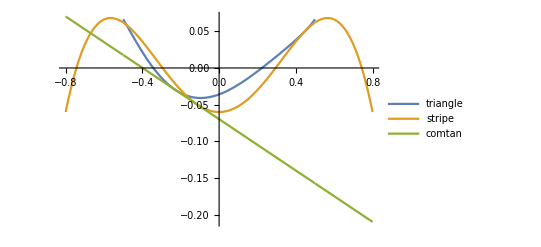

```mathematica
Subscript[ϵ, eg]=-0.6;
comtansol=FindRoot[{D[Ftr[ntr,Subscript[ϵ, eg]],ntr]==D[Fst[nst,Subscript[ϵ, eg]],nst],D[Fst[nst,Subscript[ϵ, eg]],nst]==(Ftr[ntr,Subscript[ϵ, eg]]-Fst[nst,Subscript[ϵ, eg]])/(ntr-nst)},{ntr,-0.1},{nst,0.0}]
comtanline[n0_]:=Ftr[ntr,Subscript[ϵ, eg]]+D[Ftr[ntr,Subscript[ϵ, eg]],ntr](n0-ntr)/.comtansol;
Plot[{Ftr[n0,Subscript[ϵ, eg]],Fst[n0,Subscript[ϵ, eg]],comtanline[n0]},{n0,-.8,.8},PlotLegends->{"triangle","stripe","comtan"}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

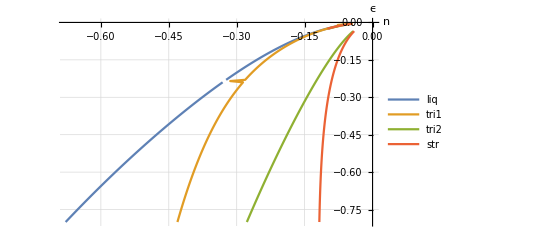

```mathematica
calPhad[ϵ_]:={nlq, ntr1, ntr2, nst}/.Join[FindRoot[{D[Flq[nlq,ϵ],nlq]==D[Ftr[ntr1,ϵ],ntr1],D[Flq[nlq,ϵ],nlq]==(Flq[nlq,ϵ]-Ftr[ntr1,ϵ])/(nlq-ntr1)},{nlq,-0.5},{ntr1,-0.3}],FindRoot[{D[Ftr[ntr2,ϵ],ntr2]==D[Fst[nst,ϵ],nst],D[Ftr[ntr2,ϵ],ntr2]==(Ftr[ntr2,ϵ]-Fst[nst,ϵ])/(ntr2-nst)},{ntr2,-0.1},{nst,-0.0}]];
data = Transpose[calPhad[#]&/@Range[-0.8,0,.005]];
epsilon = Range[-0.8,0,.005];
ListLinePlot[Transpose[{#,epsilon}]&/@data,AxesLabel->{"n","ϵ"}, PlotLegends->{"liq","tri1","tri2","str"},GridLines->Automatic]
```

```mathematica
(4 (-3 a^4 n+√3 √(-5 a^8-12 a^8 n^2+40 a^6 π^2-80 a^4 π^4-5 a^8 ϵ)))/(15 a^4)/.a->2π
```

(-48 n π^4+√3 √(-3072 n^2 π^8-1280 π^8 ϵ))/(60 π^4)

```mathematica
Simplify[(-48 n π^4+√3 √(-3072 n^2 π^8-1280 π^8 ϵ))/(60 π^4)]
```

4/15 (-3 n+√3 √(-12 n^2-5 ϵ))

```mathematica
(2 √(-a^4-3 a^4 n^2+8 a^2 π^2-16 π^4-a^4 ϵ))/(√3 a^2)/.a->2π
```

(√(-48 n^2 π^4-16 π^4 ϵ))/(2 √3 π^2)

```mathematica
Simplify[(√(-48 n^2 π^4-16 π^4 ϵ))/(2 √3 π^2)]
```

2 √(-n^2-ϵ/3)